```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/good_fits

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
δδ[r_]:=Exp[- λ r^2];
m=938.92;mh2=m/(197.327)^2; hc=197.3269631;
Vα0[α0_,r_] :=α0  δδ[r];
```

```mathematica
Scatt1[α0_?NumberQ,rmax_?NumberQ]:=Block[{f,w},
c0=α0;
f=Replace[w,NDSolve[{w'[r]+w[r]^2-mh2 Vα0[α0,r]==0,w[0]==10^20},w,{r,0,rmax}]⟦1,1⟧];rmax-f[rmax]^-1]
Scatt2[α0_?NumberQ]:=(*JPhysB:AMO 36,4055(2003),3.1*)Block[{f,θ},f=Replace[θ,NDSolve[{θ'[ϕ]==m Sec[ϕ]^4 Sin[θ[ϕ]-ϕ]^2  Vα0[α0,Tan[ϕ]],θ[0]==0},θ,{ϕ,0,π/2},AccuracyGoal->40]⟦1,1⟧];Tan[f[π/2]]]
```

```mathematica
δδ[r_]:=Exp[-λ r^2];
Vα0[α0_,r_] :=α0  δδ[r];Vα1[r_] := δδ[r];Vβ1[r_]  :=  r^2 δδ[r];


δδ[r_]:=(λ/π)^(3/2) Exp[- λ r^2];
δδ[r_]:=Exp[- λ r^2];
m=938.92;mh2=m/(197.327)^2; hc=197.3269631;
(*m=1;mh2=1; hc=1;*)
R=10;
(*anlo=1.;*)
anlo={2.0,5.0,10}[[3]];
(*anlo(3S1)=5.441 fm = 0.0275735 MeV^-1;*)
(*anlo(1S0)=-23.748 = -0.120348 MeV^-1;*)
Λl=Range[4,20,2.0];
aleph =anlo^-1;
LEC0s={};
αs={};
λs={};
ratio={};
Print["λ    a_2   C0"]
Do[{λ=Λl⟦j⟧;
C0=x/.FindRoot[Scatt1[x,R]^-1==aleph,{x,0.}];
AppendTo[LEC0s,    { StringPadRight[ToString[Λl⟦j⟧],6],StringPadRight[ToString[C0],12]}];
AppendTo[λs,    λ];
Print[StringPadRight[ToString[λ],5]<>"  "<>StringPadRight[ToString[aleph^-1],7]<>"  "<>StringPadRight[ToString[C0],7] ];
},{j,Length[Λl]}];
list=ExportString[LEC0s,"Table"]
DeleteFile["./tmp.dat"];
WriteString["./tmp.dat",list];
Close["./tmp.dat"];
```

λ    a_2   C0

NDSolve::ndsz: At r == 10., step size is effectively zero; singularity or stiff system suspected.

4.     10       -471.53

NDSolve::ndsz: At r == 10., step size is effectively zero; singularity or stiff system suspected.

6.     10       -699.74

NDSolve::ndsz: At r == 10., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

8.     10       -927.08

10.    10       -1153.8

12.    10       -1380.2

14.    10       -1606.3

16.    10       -1832.1

18.    10       -2057.7

20.    10       -2283.2

4.    	-471.537    
6.    	-699.747    
8.    	-927.082    
10.   	-1153.86    
12.   	-1380.23    
14.   	-1606.31    
16.   	-1832.15    
18.   	-2057.79    
20.   	-2283.26

NDSolve::ndsz: At r == 1.1975, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1.18468, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1.17222, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

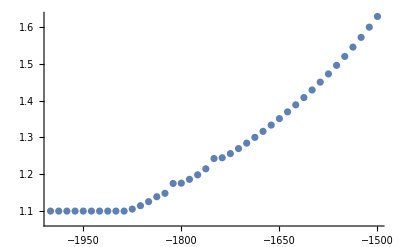

```mathematica
rma=1.2;
re=1.1;
Scatt1[α0_?NumberQ,rmax_?NumberQ,rex_?NumberQ]:=Block[{f,w},
c0=α0;
f=Replace[w,NDSolve[{w'[r]+w[r]^2-mh2 c0 Exp[-4 r]==0,w[0]==10^20},w,{r,0,rmax},Method->{"StiffnessSwitching", Method->{"ExplicitRungeKutta", Automatic}}, AccuracyGoal->2,PrecisionGoal->2]⟦1,1⟧];rex-f[rex]^-1]
V0range=Subdivide[-1500,-2000,40];
AofV=Table[Scatt1[V0range[[nn]],rma,re],{nn,Range[Length[V0range]]}];
data=Transpose[{V0range,AofV}];
ListPlot[data]
```